```mathematica
h[x_]:=Piecewise[{{1+c01 x+c02 x^2+c03 x^3+c04 x^4, 0≤x≤1}, {c11(x-1)+c12(x-1)^2+c13(x-1)^3+c14(x-1)^4, 1<x≤2}, {0, True}}];
f[x_]:=h[Abs[x]];
```

```mathematica
(*Interpolant constraints*)
I1=f[1]
I2=f[2]
```

1+c01+c02+c03+c04

c11+c12+c13+c14

```mathematica
(*Partition of unity and gradient representation*)
T0=CoefficientList[FullSimplify[f[x+1]+f[x]+f[x-1]+f[x-2],x>0&&x<1],x]
T1=CoefficientList[FullSimplify[-f[x+1]+f[x-1]+2f[x-2],x>0&&x<1],x]
```

{2+c01+c02+c03+c04+c11+c12+c13+c14,-2 c02-3 c03-4 c04-2 c12-3 c13-4 c14,2 c02+3 c03+4 c04+2 c12+3 c13+4 c14+2 (c04+c14),-4 (c04+c14),2 (c04+c14)}

{1+c01+c02+c03+c04+2 c11+2 c12+2 c13+2 c14,-c01-2 c02-3 c03-4 c04-3 c11-4 c12-6 c13-8 c14,c02+3 c03+6 c04+c12+6 c13+12 c14,-c03-4 c04-3 c13-8 c14,c04+c14}

```mathematica
GenSols=Solve[{
	I1==0,
	I2==0,
	T0[[1]]==1,
	T0[[2]]==0,
	T0[[3]]==0,
	T1[[1]]==0,
	T1[[2]]==1,
	T1[[3]]==0,
	T1[[4]]==0
	},
	{c01,c02,c03,c04,c11,c12,c13,c14}
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c04→-1-c01-c02-c03,c11→-5/3-(5 c01)/3-(2 c02)/3-c03/3,c12→2+2 c01+c02+c03,c13→-4/3-(4 c01)/3-(4 c02)/3-(5 c03)/3,c14→1+c01+c02+c03}}

```mathematica
GenSol=GenSols[[1]];
f[x_,y_]:=f[x]f[y];
φ=1/2;
W1[k_]:=Piecewise[{{0, k<0}, {φ^2/2, k==0}, {1-(1-φ)^2/2, k==1}, {1, True}}];
SumF1=∑_(i=-3)^5 ∑_(j=-3)^5 W1[i-j]f[x-i,y-j]/.GenSol;
{SumF1a1,SumF1a2,SumF1a3,SumF1a4}=Parallelize[{
	Simplify[SumF1,x>0&&x<1&&y>0&&y<1],
	Simplify[SumF1,x>0&&x<1&&y>1&&y<2],
	Simplify[SumF1,x>-1&&x<0&&y>1&&y<2],
	Simplify[SumF1,x>-1&&x<0&&y>2&&y<3]}];
{DSumF1a1,DSumF1a2,DSumF1a3,DSumF1a4}=Parallelize[{
	FullSimplify[D[SumF1a1,{{x,y}}]],
	FullSimplify[D[SumF1a2,{{x,y}}]],
	FullSimplify[D[SumF1a3,{{x,y}}]],
	FullSimplify[D[SumF1a4,{{x,y}}]]}];
{SumF1b1,SumF1b2,SumF1b3,SumF1b4}=Parallelize[{
	Simplify[SumF1,x>1&&x<2&&y>0&&y<1],
	Simplify[SumF1,x>1&&x<2&&y>-1&&y<0],
	Simplify[SumF1,x>2&&x<3&&y>-1&&y<0],
	Simplify[SumF1,x>2&&x<3&&y>-2&&y<-1]}];
{DSumF1b1,DSumF1b2,DSumF1b3,DSumF1b4}=Parallelize[{
	FullSimplify[D[SumF1b1,{{x,y}}]],
	FullSimplify[D[SumF1b2,{{x,y}}]],
	FullSimplify[D[SumF1b3,{{x,y}}]],
	FullSimplify[D[SumF1b4,{{x,y}}]]}];
```

```mathematica
{Err1a1,Err1a2,Err1a3,Err1a4,Err1b1,Err1b2,Err1b3,Err1b4}=Parallelize[{
	Simplify[∫_0^1 ∫_0^1 (DSumF1a1.{1,1})^2 ⅆxⅆy],
	Simplify[∫_1^2 ∫_0^1 (DSumF1a2.{1,1})^2 ⅆxⅆy],
	Simplify[∫_1^2 ∫_-1^0 (DSumF1a3.{1,1})^2 ⅆxⅆy],
	Simplify[∫_2^3 ∫_-1^0 (DSumF1a4.{1,1})^2 ⅆxⅆy],
	Simplify[∫_0^1 ∫_1^2 (DSumF1b1.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-1^0 ∫_1^2 (DSumF1b2.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-1^0 ∫_2^3 (DSumF1b3.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-2^-1 ∫_2^3 (DSumF1b4.{1,1})^2 ⅆxⅆy]
}];
```

```mathematica
Err1=FullSimplify[Err1a1+Err1a2+Err1a3+Err1a4+Err1b1+Err1b2+Err1b3+Err1b4];
```

```mathematica
Err=FullSimplify[Err1 /.φ->1/2]
DErr=FullSimplify[D[Err,{{c01,c02,c03}}]];
H=FullSimplify[D[Err,{{c01,c02,c03},2}]];
NSols=NSolve[DErr==0,{c01,c02,c03},Reals]
TableForm[{Range[Length[NSols]],Err/.NSols,PositiveDefiniteMatrixQ[H/.N[#]]&/@NSols}ᵀ]
```

1/6350400(2 (14121001+4601736 c01^4+4 c01^3 (6646912+2075877 c02)+6 c01^2 (9235274+c02 (6080303+945524 c02))+6 c01 (7852793+c02 (8567389+16 c02 (174999+18160 c02)))+c02 (22099269+4 c02 (3006474+c02 (648409+51042 c02))))+2 (8555243+c01 (19760445+2 c01 (6949914+1567813 c01))+9321723 c02+6 c01 (2148514+721303 c01) c02+6 (500663+336310 c01) c02^2+319400 c02^3) c03+2 (1840904+838616 c01^2+c02 (1175017+190430 c02)+c01 (2508664+791074 c02)) c03^2+4 (77435+52438 c01+25600 c02) c03^3+10461 c03^4)

{{c01→-0.617904,c02→-0.432006,c03→0.1175}}

1 | 0.0493978 | True

```mathematica
(*Bugged without the Reals dimain restriction*)
Err=FullSimplify[Err1 /.φ->1/2]
DErr=FullSimplify[D[Err,{{c01,c02,c03}}]];
H=FullSimplify[D[Err,{{c01,c02,c03},2}]];
Sols=Solve[DErr==0,{c01,c02,c03},Reals];
TableForm[{Range[Length[Sols]],Err/.N[Sols],PositiveDefiniteMatrixQ[H/.N[#]]&/@Sols}ᵀ]
```

1/6350400(2 (14121001+4601736 c01^4+4 c01^3 (6646912+2075877 c02)+6 c01^2 (9235274+c02 (6080303+945524 c02))+6 c01 (7852793+c02 (8567389+16 c02 (174999+18160 c02)))+c02 (22099269+4 c02 (3006474+c02 (648409+51042 c02))))+2 (8555243+c01 (19760445+2 c01 (6949914+1567813 c01))+9321723 c02+6 c01 (2148514+721303 c01) c02+6 (500663+336310 c01) c02^2+319400 c02^3) c03+2 (1840904+838616 c01^2+c02 (1175017+190430 c02)+c01 (2508664+791074 c02)) c03^2+4 (77435+52438 c01+25600 c02) c03^3+10461 c03^4)

1 | 0.0493978 | True

```mathematica
(*Huge in symbolic form*)
N[Sols[[1]]]
```

{c01→-0.617904,c02→-0.432006,c03→0.1175}

```mathematica
RootReduce[Sols[[1]]]
```

$Aborted

{c04→-0.0675902,c11→-0.38799,c12→0.449686,c13→-0.129287,c14→0.0675902,c01→-0.617904,c02→-0.432006,c03→0.1175}

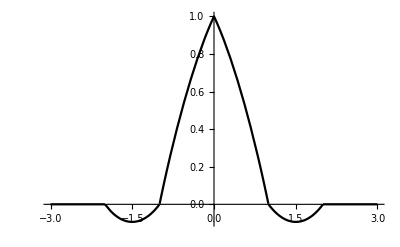

```mathematica
Sol=N[Sols[[1]]];
FullSol=N[Join[GenSol/.Sol,Sol]]
fo[x_]:=f[x]/.FullSol;
Plot[fo[x],{x,-3,3},PlotStyle->Black,Background->White]
```